```mathematica
ClearAll["Global`*"]
```

```mathematica
L=1;
h=0.2;
R=L/Sqrt[2];
c={L/2,h+L/2};
```

```mathematica
u1[x_]:=x^2
```

```mathematica
(*read u_1*)
```

```mathematica
t1=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/two_domains/solution/u_1_test.csv"];
t1=Table[{t1[[i,2]],t1[[i,1]]},{i,2,Length[t1]}]
```

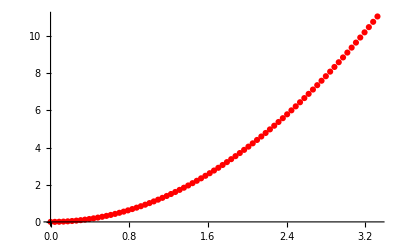

```mathematica
plotu1=ListPlot[t1,PlotStyle->Red]
```

```mathematica
Solve[{3π/2 a + b ==π+π/4,-3 π/2(1-a)+b==-π/4},{a,b}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{b→(5 π)/4-(3 a π)/2}}

```mathematica
plotu1on0=ParametricPlot3D[{c[[1]]+R Cos[-3π/2 t+5π/4],c[[2]]+R Sin[-3π/2 t+5π/4],u1[3π /2 R t]},{t,0,1},PlotStyle->Blue,AspectRatio->Full]
```

-Graphics3D-

```mathematica
(*read u_0*)
```

```mathematica
t0=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/two_domains/solution/u_0_test.csv"];
t0=Table[{t0[[i,2]],t0[[i,3]],t0[[i,1]]},{i,2,Length[t0]}]
```

```mathematica
plotu0=ListPointPlot3D[t0,PlotStyle->{Green,PointSize->0.01}]
```

-Graphics3D-

```mathematica
Show[plotu0,plotu1on0,PlotRange->Full]
```

-Graphics3D-